```mathematica
CellPrint[Cell["Directory","Section"]]
CellPrint[Cell["Main code & XZ independent noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"general_codes.nb"],Appearance->"DialogBox"]
CellPrint[Cell["DATA & code definitions :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"data_summary.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depoloarizing Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Approxiating polynomials:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"approximating_polynomials.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depolarizing noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ (symmetric) noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise_ME.nb"],Appearance->"DialogBox"]
SetDirectory[NotebookDirectory[]]
```

## Directory

Main code & XZ independent noise:

DATA & code definitions :

Depoloarizing Noise:

XZ uneven Noise:

Approxiating polynomials:

Depolarizing noise with Measurement error :

XZ (symmetric) noise with Measurement error :

XZ uneven noise with Measurement error :

/Users/naomi/Dropbox/&Projects/Small codes

## Directory

Main code & XZ independent noise:

DATA & code definitions :

Depoloarizing Noise:

XZ uneven Noise:

Approxiating polynomials:

Depolarizing noise with Measurement error :

XZ (symmetric) noise with Measurement error :

XZ uneven noise with Measurement error :

/Users/naomi/Dropbox/&Projects/Small codes

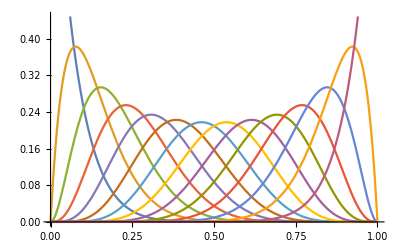

```mathematica
bin=Table[Binomial[13,n]*(1-p)^(13-n)*p^n,{n,0,13}];
Plot[%,{p,0,1}]
```

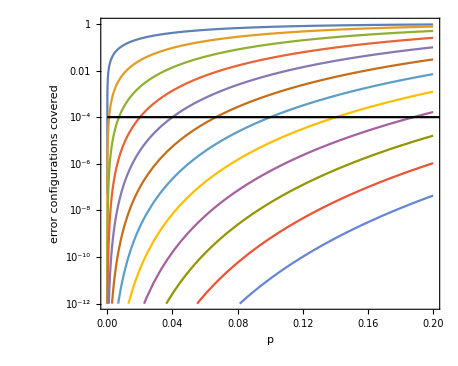

```mathematica
test=1-Plus@@bin[[1;;#]]&/@Range[12];
Show[LogPlot[test,{p,0,0.2},PlotRange->{{0,0.2},{10^-12,1}}],
ListLogPlot[{{0,10^-4},{1,10^-4}},Joined->True,PlotStyle->Black],Frame->True,FrameLabel->{"p","error configurations covered"},LabelStyle->15,AspectRatio->0.8]
```

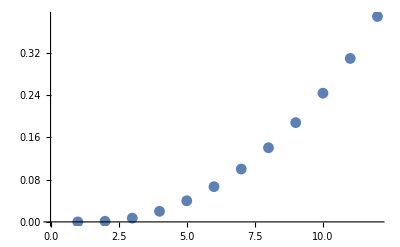

```mathematica
p/.Solve[#==0.0001,p,Reals]&/@test;
Select[Flatten@%,0<#&&#≤1&];
ListPlot[%]
```

```mathematica
planar5=<<"planar5.txt";
```

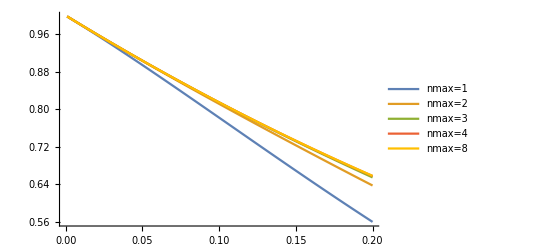

```mathematica
Show[plotResultsF[truncatePolynomials[planar5,#],5,successRate,#,StringJoin["nmax=",ToString[#]]]&/@{1,2,3,4,8}]
```

## approximating the 9 qubit surface code

```mathematica
planar9=<<"planar9.txt";

plotPlanar9=plotResultsF[truncatePolynomials[planar9,,9,successRate,5,"planar 9"]
```

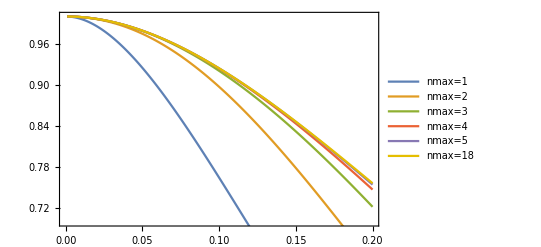

```mathematica
p1=Show[plotResultsF[truncatePolynomials[planar9,#],9,successRate,#,StringJoin["nmax=",ToString[#]]]&/@{1,2,3,4,5,18},PlotRange->{{0,0.2},{0.7,1}},

Frame->True]
```

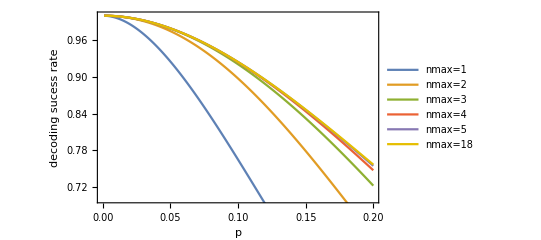

```mathematica
Show[p1,FrameLabel->{"p","decoding sucess rate"},LabelStyle->15,AspectRatio->0.6]
```